```mathematica
遗传算法
```

写在前面:自从公众号开了以后,我每天都在思考下一个主题是什么,怎么写会比较有趣. 但是由于每天时间以及公众号的推送篇幅有限(太长了大家也不会看), 我没有办法深挖一个主题, 每次都是打一枪换一个地方. 

我喜欢深挖一个主题.

所以从今天的推送开始,可能很多期都会讲同一个主题.

另外我想尝试一下直接用Mathematica Notebook来做分享,一是它排版方便,比微信的原生排版系统要方便, 二是可以节省一些功夫.

正文 : 假设我们有这么一组数据

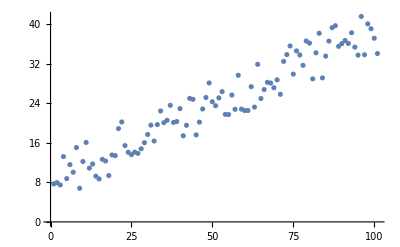

```mathematica
y=Table[3x+4+RandomReal[10],{x,0,10,0.1}];
ListPlot[y]
```

我们想要用遗传算法找到一条线能够最佳地拟合这些数据.
第一步. 设定根算法.  
随机生成20条算法(染色体):

```mathematica
chromosomes=SetPrecision[Table[{RandomReal[10],RandomReal[10]},20],3]
```

{{0.874,2.05},{1.11,9.78},{5.61,4.03},{0.432,2.44},{1.26,6.02},{2.28,6.85},{4.05,5.81},{4.43,4.45},{6.5,5.81},{5.38,5.28},{0.983,6.24},{8.,3.99},{5.16,7.46},{2.73,5.96},{7.26,7.57},{8.06,3.74},{1.62,4.82},{3.35,8.17},{4.62,0.921},{1.46,1.9}}

接下来, 我们需要将每一只染色体用二进制来表达

```mathematica
chromosomes~BaseForm~2
```

{{0.1101111111_2,10.00001100_2},{1.000111010_2,1001.110010_2},{101.1001110_2,100.0000011_2},{0.01101110101_2,10.01101111_2},{1.010000101_2,110.0000010_2},{10.01001000_2,110.1101100_2},{100.0000110_2,101.1101000_2},{100.0110111_2,100.0111001_2},{110.0111111_2,101.1101000_2},{101.0110000_2,101.0100100_2},{0.111111000_2,110.0011111_2},{1000.000000_2,11.1111111_2},{101.0010100_2,111.0111011_2},{10.10111011_2,101.1111010_2},{111.0100010_2,111.1001001_2},{1000.000100_2,11.10111100_2},{1.101000000_2,100.1101001_2},{11.01011001_2,1000.001011_2},{100.1001111_2,0.1110101111_2},{1.011101010_2,1.111001011_2}}

我们可以把他们视觉化,使得每一行都是一条染色体

```mathematica
ArrayPlot[ArrayReshape[Map[RealDigits[#,2,9][[All,1]]&,chromosomes],{20,9*2}]]
```

-Graphics-

现在我们要设计一个适合函数，筛选出前10名。
这个函数很简单，就是用最小二乘法算出的误差值。

```mathematica
Fitness[w_]:=
Module[{x=Table[{i,1},{i,0,10,0.1}]},
Return[Total[(y-x.w)^2]]
]
```

```mathematica
Fitness[{1.2,3.2}]
```

25374.2

```mathematica
choices=Ordering[Map[Fitness,chromosomes]][[1;;10]]
```

{18,7,14,19,8,6,2,10,3,13}

有了前10个最好的染色体之后，我们选出他们进行交配（cross over），没错，交配。交配的过程是这样的：每只染色体随机的取出一半的DNA，也就是bits，然后经过一定几率(10%）的变异，结合成新的染色体。每两个染色体交配后生育下两个染色体，这两个染色体的DNA互异又互补。也就是说，父母的DNA一半分到一个子染色体，一半分到另一个子染色体。(下期待续)